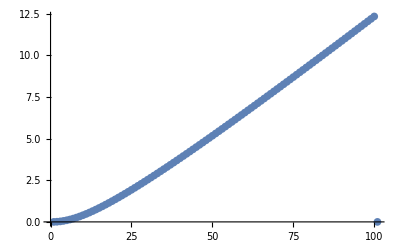

0

```mathematica
j[x_]:=0;
f[x_]:=ArcTan[x];
y0 = f[0];
h = 0.1;
tab2= Table[j[x],{x,0,10,h}];
tab2[[1]]=0;
For[i=2, i≤100, i++,
tab2[[i]] = tab2[[i-1]]+h*ArcTan[h*(i-1)]]

ListPlot[tab2]
tab2[[1]]
```